```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=If[s==0,-2Log[m],If[s==4 m^2,2-2Log[m],2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]]] ;
ScalarFPrime0[m_,s_]:=If[s==4 m^2,-1/(4 m^2),-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))ArcTan[(√s)/(√(4 m^2-s))]];
PropagatorScalar[s_,M_,m_,c_,Γ_]:=1/(s-M^2+ⅈ×M×Γ+c×(ScalarF0[m,s]-ScalarF0[m,M^2]-(s-M^2)Re[ScalarFPrime0[m,M^2]]));
```

```mathematica
FermionF0[m_,s_]:=If[s==0,4 m^2-s,If[s==4 m^2,0,((4 m^2-s)^(3/2))/(√s)ArcTan[(√s)/(√(4 m^2-s))]]] ;
FermionFPrime0[m_,s_]:=If[s==4 m^2,0,(4 m^2-s)/(2s)-((2 m^2+s) √(4 m^2-s))/s^(3/2)ArcTan[(√s)/(√(4 m^2-s))]];
PropagatorFermion[s_,M_,m_,c_,Γ_]:=1/(s-M^2+ⅈ×M×Γ+c×(FermionF0[m,s]-FermionF0[m,M^2]-(s-M^2)Re[FermionFPrime0[m,M^2]]));
```

```mathematica
50000/Im[ScalarF0[100,1000^2]]//N
```

16243.7

```mathematica
50000/Im[FermionF0[100,1000^2]]//N
```

0.033841

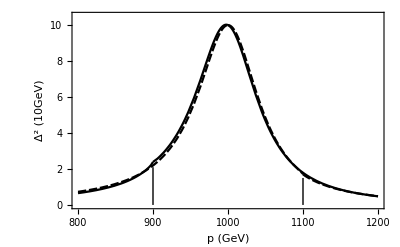

```mathematica
Plot[{10^11×Abs[PropagatorScalar[p^2,1000,450,16243.7,100]]^2,10^11×Abs[PropagatorScalar[p^2,1000,550,16243.7,100]]^2},{p,800,1200},PlotRange->{0,10.5},MaxRecursion->15,PlotTheme->"Monochrome",LabelStyle->{14,FontFamily->"Times New Roman"},Axes->False,Frame->{{True,False},{True,False}},PlotRangePadding->0,FrameLabel->{{Style[StringForm["`` (````)",Abs[Δ[p^2]]^2,Superscript[10,-11],Superscript[GeV,-4]],16],None},{Style[StringForm["`` (``)",Abs[p],GeV],16],None}},Epilog->{Thin,Line[{{900,2.1},{900,0}}],Line[{{1100,1.5},{1100,0}}],Transparent,EdgeForm[Thin],Rectangle[{896,2.1},{904,2.5}],Rectangle[{1096,1.5},{1104,1.9}],Inset[Plot[10^11×Abs[PropagatorScalar[p^2,1000,450,16243.7,100]]^2,{p,896,904},PlotRange->{2.1,2.5},Frame->True,FrameTicks->None,PlotRangePadding->0,MaxRecursion->15,AspectRatio->1.2,ImageSize->60,PlotTheme->"Monochrome"],{880,7}],Inset[Plot[10^11×Abs[PropagatorScalar[p^2,1000,550,16243.7,100]]^2,{p,1096,1104},PlotRange->{1.5,1.9},FrameTicks->None,PlotRangePadding->0,Frame->True,MaxRecursion->15,AspectRatio->1.2,ImageSize->60,PlotStyle->Dashing[{0.08,0.02}],PlotTheme->"Monochrome"],{1120,7}]}]
```

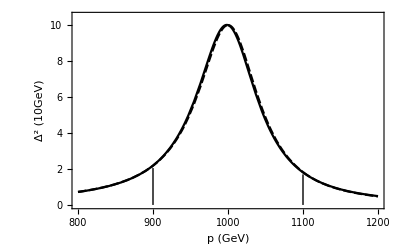

```mathematica
Plot[{10^11×Abs[PropagatorFermion[p^2,1000,450,0.033841,100]]^2,10^11×Abs[PropagatorFermion[p^2,1000,550,0.033841,100]]^2},{p,800,1200},PlotRange->{0,10.5},MaxRecursion->15,PlotTheme->"Monochrome",LabelStyle->{14,FontFamily->"Times New Roman"},Axes->False,Frame->{{True,False},{True,False}},PlotRangePadding->0,FrameLabel->{{Style[StringForm["`` (````)",Abs[Δ[p^2]]^2,Superscript[10,-11],Superscript[GeV,-4]],16],None},{Style[StringForm["`` (``)",Abs[p],GeV],16],None}},Epilog->{Thin,Line[{{900,2.05},{900,0}}],Line[{{1100,1.7},{1100,0}}],Transparent,EdgeForm[Thin],Rectangle[{896,2.05},{904,2.35}],Rectangle[{1096,1.7},{1104,2.0}],Inset[Plot[10^11×Abs[PropagatorFermion[p^2,1000,450,0.033841,100]]^2,{p,896,904},PlotRange->{2.05,2.35},Frame->True,FrameTicks->None,PlotRangePadding->0,MaxRecursion->15,AspectRatio->1.2,ImageSize->60,PlotTheme->"Monochrome"],{880,7}],Inset[Plot[10^11×Abs[PropagatorFermion[p^2,1000,550,0.033841,100]]^2,{p,1096,1104},PlotRange->{1.7,2.0},FrameTicks->None,PlotRangePadding->0,Frame->True,MaxRecursion->15,AspectRatio->1.2,ImageSize->60,PlotStyle->Dashing[{0.08,0.02}],PlotTheme->"Monochrome"],{1120,7}]}]
```